# Full transition probability function

```mathematica
ThatFactorialTerm[p_]:=Times@@Factorial[Tally[p]][[All,2]];
FullTP[n_,N_,k_,d_]:=
Module[{P,Q,Mp,Mq},
P=IntegerPartitions[k+d];
Q=IntegerPartitions[n-k-d];
Binomial[n,k+d]Total[Table[
(1/N)^(n-Length[p]-Length[q])Product[1-i/N,{i,1,Length[p]+Length[q]-1}]
(Multinomial@@q)/ThatFactorialTerm[q]
(Multinomial@@p)/ThatFactorialTerm[p]
Binomial[n-Length[p]-Length[q],n-k-Length[q]]/Binomial[n,k],{p,P},{q,Q}],{1,2}]]
```

```mathematica
FullTP[8,75,5,3]
```

3521613499/83056640625000

```mathematica
t=Table[FullTP[20,10000,k,l-k],{k,0,20},{l,0,20}];
```

```mathematica
Total[t,{2}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

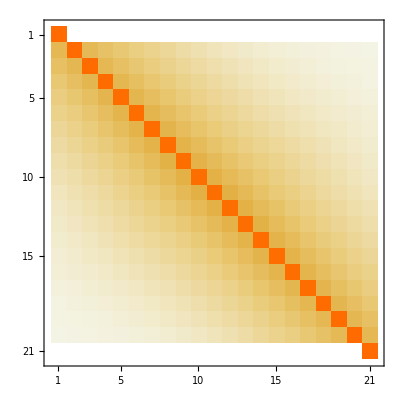

```mathematica
MatrixPlot[t]
```

## Simple coalescence only - {1,2}

```mathematica
SimpleTP[n_,N_,k_,d_]:=
Module[{P,Q,Mp,Mq},
P=IntegerPartitions[k+d,All,{1,2}];
Q=IntegerPartitions[n-k-d,All,{1,2}];
Binomial[n,k+d]Total[Table[
(1/N)^(n-Length[p]-Length[q])Product[1-i/N,{i,1,Length[p]+Length[q]-1}]
(Multinomial@@q)/ThatFactorialTerm[q]
(Multinomial@@p)/ThatFactorialTerm[p]
Binomial[n-Length[p]-Length[q],n-k-Length[q]]/Binomial[n,k],{p,P},{q,Q}],{1,2}]]
```

```mathematica
s=Table[SimpleTP[20,10000,k,l-k],{k,0,20},{l,0,20}];
```

```mathematica
Total[s,{2}]//N
```

{0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989,0.999989}

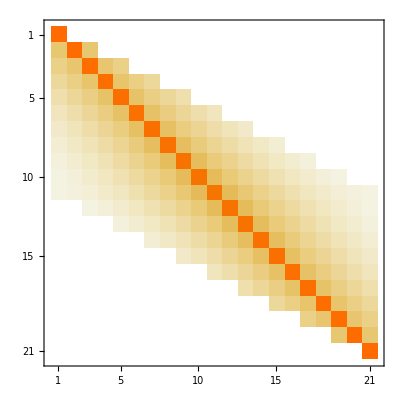

```mathematica
MatrixPlot[s]
```